# Project report

## Aromatics in diesel: spiked and not spiked

D Malan

Department of Chemistry
University of Pretoria

11 February 2020

## Introduction

Two SFC×GC runs of diesel that shows aromatics.

## Experimental

### Conditions

Sampling period/modulation period: 3s

### Sample 1

10% PAHs in diesel Total™ 50 ppm

```mathematica
aromatics ={"Cumene", "1,4-diisopropylbenzene","Bibenzyl", "Naphthalene", "Anthracene", "Chrysene", "BenzoApyrene"}
```

{Cumene,1,4-diisopropylbenzene,Bibenzyl,Naphthalene,Anthracene,Chrysene,BenzoApyrene}

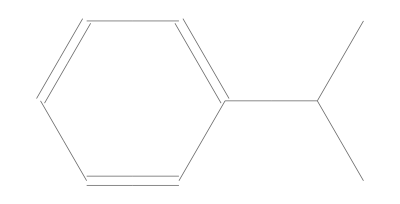
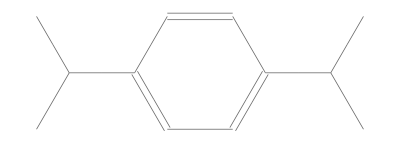
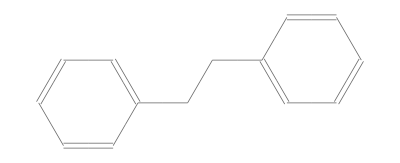
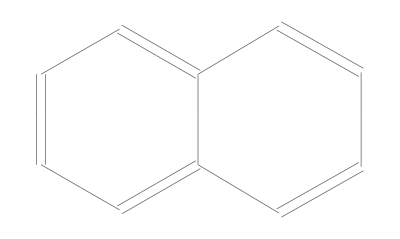
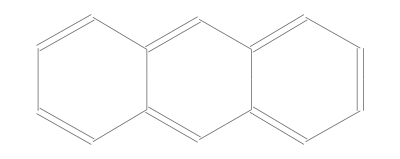
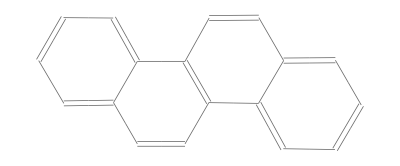
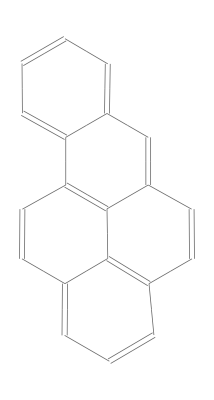
-Graphics- | cumene | 153. °C
-Graphics- | 1,4-diisopropylbenzene | 210. °C
-Graphics- | bibenzyl | 284. °C
-Graphics- | naphthalene | 218. °C
-Graphics- | anthracene | 340. °C
-Graphics- | chrysene | 448. °C
-Graphics- | benzo[a]pyrene | 495. °C

```mathematica
TableForm[{ChemicalData[#], ChemicalData[#, "Name"], ChemicalData[#, "BoilingPoint"]}&/@ aromatics ]
```

### Sample 2

Engen 500 ppm

This sample has a total aromatics content of 0.32%

## Calculations

## Results

### Sample 1

```mathematica
"C:\\SFC-GC\\Data\\2020_02_11-120014.dat"
```

### Sample 2

```mathematica
"C:\\SFC-GC\\Data\\2020_02_11-132105.dat"
```

-Graphics3D-

## Discussion

The SFC×GC instrument ran without trouble, and each chromatogram was completed in 75 minutes. The longer sampling period (3s instead of 2s) makes no real difference to the quality of the data, but it makes the run times shorter.

The spiked aromatic compounds are clearly visible in the chromatogram, except for the two-ring aromatics, bibenzyl and naphthalene.

### Temperature control

The chromatograms are satisfactory, but there are some cases where the temperature programs was not repeatable enough, as can be clearly seen in the peaks of the slowly-eluting carry-over peaks. The fact that there are long runs where the repeatability is good means that it is not an intrinsic problem, but something that happens on occasion.

I believe this is caused by a combination of two factors:

### 1. Non-deterministic operating system

The two graphs below shows the difference between two fast GC runs. The retention times of the two peaks differ by about 0.2 s, which is significantly larger than the peak width. The black dots shows the temperature. It is clear that there are fewer black dots on the second graph than on the first one. This is because the operating system (Windows) decided that other processes had higher priority than the SFC×GC software, so that fewer data points were recorded.

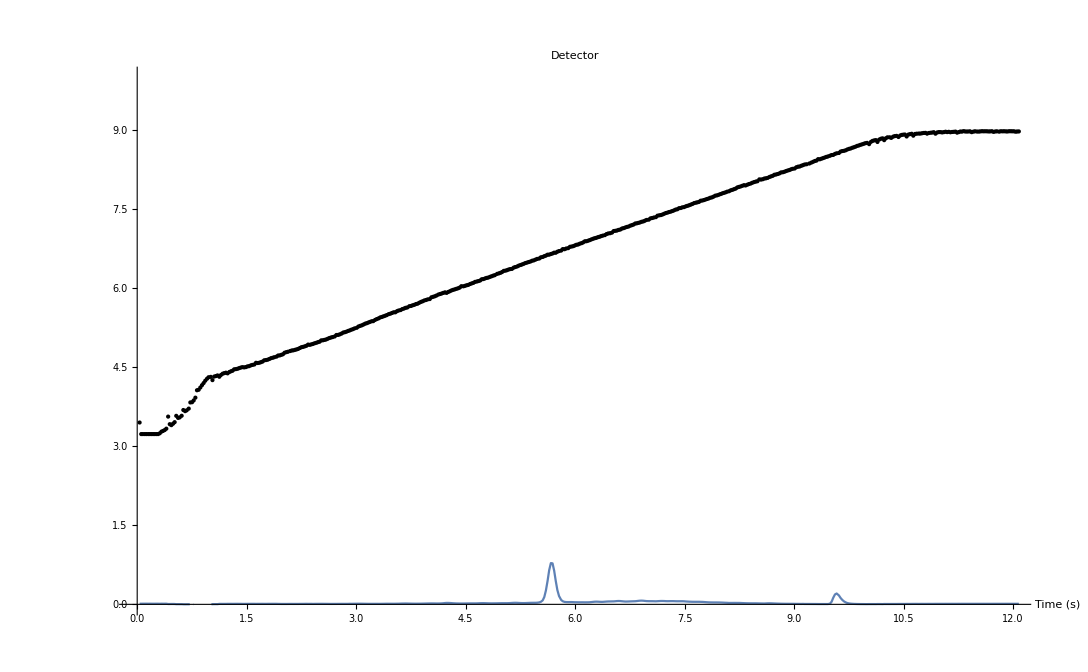

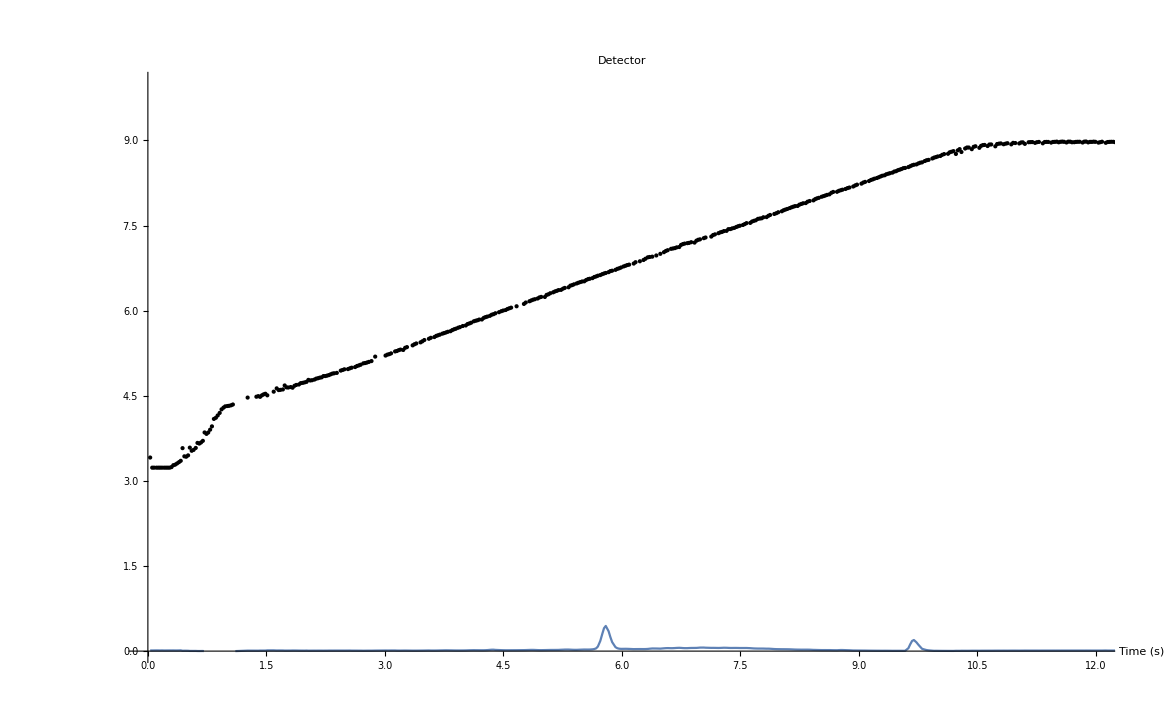

In this example, the number of points per fast GC run varied between 420 and 520. The graph below shows how this varies.

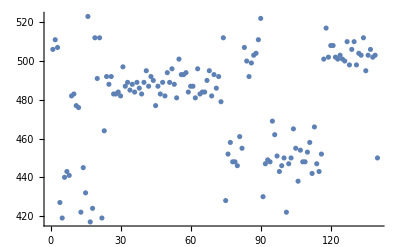

```mathematica
Length/@ data2d[[Range[Length[data2d]]]]//ListPlot
```

#### 2. Naïve calculation

In a PID controller the Integral term is calculated by summing the difference between the setpoint and the measured value. In the LabVIEW implementation a simplification was used, and it was assumed that the data points are evenly spaced. This simplifies the coding, and it works most of the time. But if data points are missed, the integral has a lower value than expected, which means that in practice less power are put to the coaxial heater, so the temperature program runs slower.

### Cryogen bleed?

The recorded temperature shows a time of  constant temperature at the beginning of the temperature ramp. This is undesirable, and is probably responsible for the rather fussy peaks at the start of the GC chromatograms. I think this might be caused by the last of the cooling CO_2 bleeding into the column through the almost-closed metering valve. It might be possible to open the metering valve more, without increasing the cooling in the manifold blocks.

## Conclusion

Chromatograms were collected that clearly shows the orthogonal separation of polycyclic aromatic hydrocarbons in commercial diesel. The influence of the number of rings on SFC retention time was demonstrated by spiking a diesel sample with a selection of PAHs.

## Recommendations

Use a real-time operating system with deterministic timing to run scientific instruments.

Use proper integration methods when calculating the I term of the PID controller.

Test a higher cryogen flow: it might be possible to sacrifice manifold block temperature for a faster start of the temperature ramp.

Use a peak alignment algorithm to improve the appearance of the chromatogram of the spiked diesel sample.